```mathematica
sf=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-n.wdx"];
ft1=Query[1,1]@sf;
ft2=Query[2,1]@sf;
gt1=Query[1,2]@sf;
gt2=Query[2,2]@sf;
```

```mathematica
fp1=Interpolation[Flatten[ft1,1]];
fp2=Interpolation[Flatten[ft2,1]];
gp1=Interpolation[Flatten[gt1,1]];
gp2=Interpolation[Flatten[gt2,1]];
```

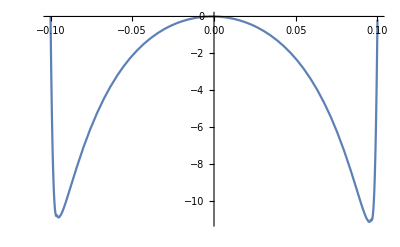

```mathematica
Plot[fp1[x,-1],{x,-0.1,0.1}]
```

```mathematica
pf1[x_]=Piecewise[{{fp1[x,-1],x<0.1},{,x>0.1}}];
pg[x_]=Piecewise[{{gp1[x,-1],x<0.1},{gp2[x,-1],x>0.1}}];
```

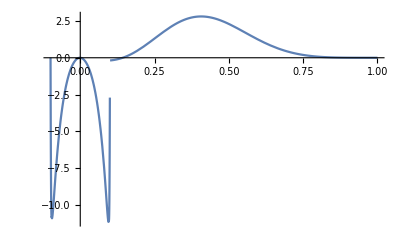

```mathematica
Plot[pf[x],{x,-0.1,1},PlotRange->All]
```

```mathematica
fp1[0.1,-1]
```

-0.182828+0. ⅈ

```mathematica
fp2[0.1,-1]
```

-0.182828

```mathematica
tpf[x_]:=If[x<0.1,fp1[x,-1],fp2[x,-1]];
```

```mathematica
Plot[tpf[x],{x,-0.1,1},PlotRange->All]
```

-Graphics-

```mathematica
tpf[0.1]
```

-0.182828

```mathematica
tpf[0.099999]
```

-0.190633+0. ⅈ

```mathematica
Show
```

```mathematica
tf1=Interpolation[Flatten[Join[ft1,ft2],1]];
```

Interpolation::indp: There are duplicated abscissa points in {{-0.1,-1.},{-0.1,-0.99},{-0.1,-0.98},{-0.1,-0.97},{-0.1,-0.96},{-0.1,-0.95},{-0.1,-0.94},{-0.1,-0.93},{-0.1,-0.92},{-0.1,-0.91},{-0.1,-0.9},{-0.1,-0.89},{-0.1,-0.88},{-0.1,-0.87},{-0.1,-0.86},{-0.1,-0.85},{-0.1,-0.84},«18»,{-0.1,-0.65},{-0.1,-0.64},{-0.1,-0.63},{-0.1,-0.62},{-0.1,-0.61},{-0.1,-0.6},{-0.1,-0.59},{-0.1,-0.58},{-0.1,-0.57},{-0.1,-0.56},{-0.1,-0.55},{-0.1,-0.54},{-0.1,-0.53},{-0.1,-0.52},{-0.1,-0.51},«28432»}.

```mathematica
lft=Join[ft1,ft2];
```

```mathematica
lft1=Delete[lft,102];
```

```mathematica
lft[[102]]
```

{{{0.1,-1.},-0.1828275165},{{0.1,-0.99},-0.1774048728},{{0.1,-0.98},-0.1717738871},{{0.1,-0.97},-0.1659274413},{{0.1,-0.96},-0.1598581452},{{0.1,-0.95},-0.1535583081},{{0.1,-0.94},-0.1470206052},{{0.1,-0.93},-0.1402345088},{{0.1,-0.92},-0.1331943499},{{0.1,-0.91},-0.1258888925},{{0.1,-0.9},-0.1183105664},{{0.1,-0.89},-0.1104489973},{{0.1,-0.88},-0.1022943574},{{0.1,-0.87},-0.09383564636},{{0.1,-0.86},-0.08506186438},{{0.1,-0.85},-0.07596200602},{{0.1,-0.84},-0.06652433093},{{0.1,-0.83},-0.05673623588},{{0.1,-0.82},-0.04658494452},{{0.1,-0.81},-0.03605725186},{{0.1,-0.8},-0.0251391105},{{0.1,-0.79},-0.01381581794},{{0.1,-0.78},-0.002072325759},{{0.1,-0.77},0.01010723396},{{0.1,-0.76},0.02273949276},{{0.1,-0.75},0.03584165292},{{0.1,-0.74},0.04943163916},{{0.1,-0.73},0.06352918621},{{0.1,-0.72},0.07815326257},{{0.1,-0.71},0.0933250814},{{0.1,-0.7},0.1090653745},{{0.1,-0.69},0.1253973657},{{0.1,-0.68},0.1423448768},{{0.1,-0.67},0.1599326318},{{0.1,-0.66},0.1781867702},{{0.1,-0.65},0.197134645},{{0.1,-0.64},0.216804992},{{0.1,-0.63},0.2372278756},{{0.1,-0.62},0.2584349952},{{0.1,-0.61},0.2804597184},{{0.1,-0.6},0.303337091},{{0.1,-0.59},0.3271035246},{{0.1,-0.58},0.3517980107},{{0.1,-0.57},0.3774613731},{{0.1,-0.56},0.404136628},{{0.1,-0.55},0.4318691589},{{0.1,-0.54},0.4607068545},{{0.1,-0.53},0.4907002795},{{0.1,-0.52},0.5219028595},{{0.1,-0.51},0.5543710841},{{0.1,-0.5},0.588164728},{{0.1,-0.49},0.6233470931},{{0.1,-0.48},0.6599852719},{{0.1,-0.47},0.6981504342},{{0.1,-0.46},0.7379181385},{{0.1,-0.45},0.779368671},{{0.1,-0.44},0.8225874153},{{0.1,-0.43},0.8676652585},{{0.1,-0.42},0.9146990368},{{0.1,-0.41},0.9637920281},{{0.1,-0.4},1.015054496},{{0.1,-0.39},1.068604292},{{0.1,-0.38},1.124567522},{{0.1,-0.37},1.183079289},{{0.1,-0.36},1.244284516},{{0.1,-0.35},1.308338854},{{0.1,-0.34},1.375409709},{{0.1,-0.33},1.445677375},{{0.1,-0.32},1.519336313},{{0.1,-0.31},1.596596591},{{0.1,-0.3},1.677685504},{{0.1,-0.29},1.762849408},{{0.1,-0.28},1.8523558},{{0.1,-0.27},1.946495681},{{0.1,-0.26},2.045586251},{{0.1,-0.25},2.149973992},{{0.1,-0.24},2.260038213},{{0.1,-0.23},2.376195137},{{0.1,-0.22},2.498902631},{{0.1,-0.21},2.628665707},{{0.1,-0.2},2.766042945},{{0.1,-0.19},2.911654025},{{0.1,-0.18},3.066188614},{{0.1,-0.17},3.230416896},{{0.1,-0.16},3.405202131},{{0.1,-0.15},3.591515716},{{0.1,-0.14},3.790455374},{{0.1,-0.13},4.00326727},{{0.1,-0.12},4.231373111},{{0.1,-0.11},4.476403618},{{0.1,-0.1},4.740240251},{{0.1,-0.09},5.025067714},{{0.1,-0.08},5.333440744},{{0.1,-0.07},5.668370026},{{0.1,-0.06},6.033434172},{{0.1,-0.05},6.432927707},{{0.1,-0.04},6.872059741},{{0.1,-0.03},7.357225416},{{0.1,-0.02},7.896384157},{{0.1,-0.01},7.790893325},{{0.1,0.},7.146662542}}

```mathematica
tf2=Interpolation[Flatten[lft1,1]];
```

```mathematica
tf2[0.1,-1]
```

-0.0778712+0. ⅈ

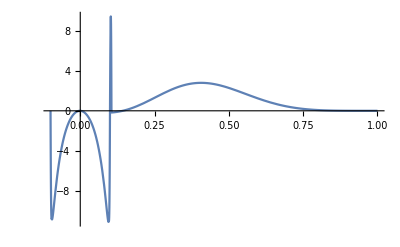

```mathematica
Plot[tf2[x,-1],{x,-0.1,1},PlotRange->All]
```

```mathematica
(0.76+0.5)^2/(2*(0.093)^2*(2π)^4)
```

0.0588879

```mathematica
yfp1[x_]=0.5*0.05888785346404517*x*fp1[x,-1];
```

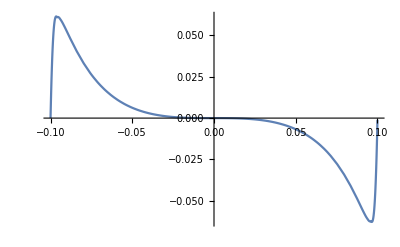

```mathematica
Plot[yfp1[x],{x,-0.1,0.1}]
```

```mathematica
sfm=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-m-n.wdx"];
ftm1=Query[1,1]@sfm;
fpm1=Interpolation[Flatten[ftm1,1]];
yfm1[x_]=0.02856607387321113*x*fpm1[x,-1];
```

```mathematica
(-2*0.76)^2/(6*(0.093)^2*(2π)^4)
```

0.0285661

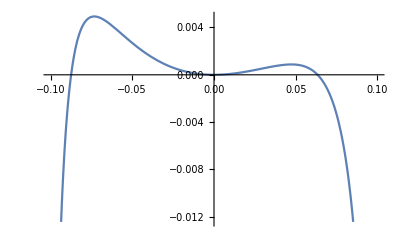

```mathematica
Plot[0.5*yfm1[x],{x,-0.1,0.1}]
```

```mathematica
sfk=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-k-n.wdx"];
ftk1=Query[1,1]@sfk;
fpk1=Interpolation[Flatten[ftk1,1]];
yfk1[x_]=0.018546187157988524*x*fpk1[x,-1];
```

```mathematica
1/(4*(0.093)^2*(2π)^4)
```

0.0185462

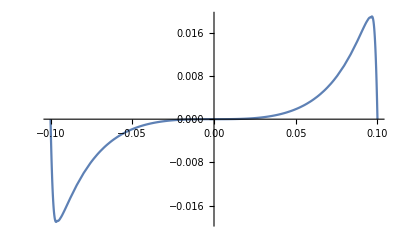

```mathematica
Plot[0.5*yfk1[x],{x,-0.1,0.1}]
```

```mathematica
sfl=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-l-n.wdx"];
gtl1=Query[1,2]@sfl;
gpl1=Interpolation[Flatten[gtl1,1]];
ygl1[x_]=0.2522281453486439*x*gpl1[x,-1];
```

```mathematica
2*(1.24+0.46)/((0.093)^2*(2π)^4)
```

0.252228

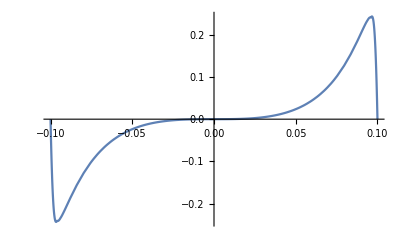

```mathematica
Plot[0.5*yfl1[x],{x,-0.1,0.1}]
```

```mathematica
gtm1=Query[1,1]@sfm;
gpm1=Interpolation[Flatten[gtm1,1]];
gfm1[x_]=0.02856607387321113*x*gpm1[x,-1];
```

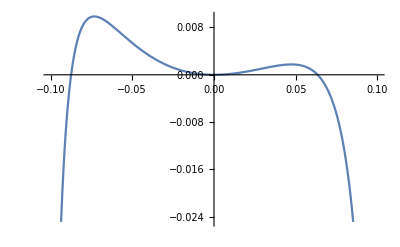

```mathematica
Plot[gfm1[x],{x,-0.1,0.1}]
```

```mathematica
ygp1[x_]=0.05888785346404517*x*gp1[x,-1];
```

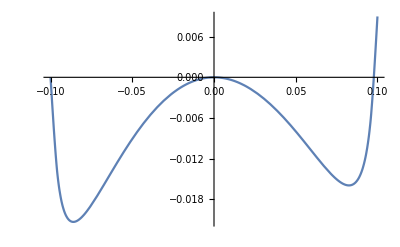

```mathematica
Plot[ygp1[x],{x,-0.1,0.1}]
```

```mathematica
Plot[fp1[x,-1],{x,-0.1,0.1}]
```

-Graphics-

```mathematica
Show[Plot3D[fp1[x,t],{x,-0.1,0.1},{t,-1,0}],Plot3D[fp2[x,t],{x,0.1,1},{t,-1,0}],AxesLabel->{"y","t","f(y)"}]
```

-Graphics3D-

```mathematica
rfp1[x_,t_]=0.5*0.05888785346404517*x*fp1[x,t];
rfp2[x_,t_]=0.5*0.05888785346404517*x*fp2[x,t];
```

```mathematica
Show[Plot3D[rfp1[x,t],{x,-0.1,0.1},{t,-1,0}],Plot3D[rfp2[x,t],{x,0.1,1},{t,-1,0}],AxesLabel->{"y","t","f(y)"}]
```

-Graphics3D-